## Principal Axis For A Bowling Ball with Different Pin-to-PAP

### Theory

Inertia Tensors are used to specifically find the rotation around any axis of a rigid body.  This is useful because the axis with which the body rotates may change with time.  Additionally, inertia tensors are used to find principle axis, which are the axis’ when the angular momentum is in the same direction as the axis of rotation.  
For Bowlers, the ideal path of a bowling ball is for the ball to “flare” which increases the chances for all the pins to fall down.  In order to do this, the bowler has to spin the bowling ball.  As the ball begins to travel down the lane, friction will cause the ball to start curving.  Manufacturers have began to take advantage of this in order to make an ideal ball.
First, I should discuss how the bowling ball is made.  There is a positive axis point (PAP) which is the initial axis of rotation as soon as it travels down the lane.  If this ball is spun correctly, the PAP will have a precession.  As the axis precesses down the lane, the ball will begin to curve.  Precession is the change in the angular velocity over time. This is the ideal motion of a bowling ball.  The PAP is due to the way the ball was manufactured.  Recently, companies have started to build asymmetrical cores in order to adjust the PAP.  
One way to get the ball to precess is to add a weight block.  A pin points out on the opposite of the weight block in the same axis.  In addition, they will add a Pin-to-PAP distance for different bowlers.  Typical distances are 1.5, 3, and 6 inches of the (x) axis.  
So in this program, I will be calculating for the different principal axis of balls with these different Pin-to-PAP distances.  I will also have a ball with a 0 Pin-to-PAP distance.
To do this, I will have to find the overall inertia tensor for the different layers of the bowling ball.  This will be done by adding each components inertia tensor together.  Then, I will use a root finder to find the principal axis of each.
10 Pin bowling balls typically have a heavy core, a weight block, and an outer core.  The inner core has a much greater mass than the outer core.  
For the asymmetric bowling ball which I will be testing for, I have decided to add a steel rectangular prism as a weight block.  The inner core is a graphite sphere.  There is a layer between the outer shell and the inner core, which I will call the inner shell.  This will fill in the gap where the weight block and pin are.  
To keep this consistent, the specifications I will be using is are as follows: 

D = Total Diameter: 22 cm
r = Inner Core Outward Length: 5 cm
R = Outer Core Outward Length: 5 cm
a = Weight Block Width: 1 cm
b = Weight Block Length: 2 cm
c = Weight Block Height: 4 cm
s = Inner Shell Radius: 1 cm
ρ = Inner Core Mass Density: 2.266 g/cm^3
p2 = Weight Block Mass Density: 7.8 g/cm^3
p3 = Inner Shell Mass Density: 1.38 g/cm^3
p4 = Outer Shell Mass Density: 1.002 g/cm^3

*Note the mass densities are uniform for each respective component.

### Inertia Tensor For Iron Block Inside Core

I have added a general formula to calculate for the inertia tensor.  Since the only thing changing is the angle of the pin/weight block, I can simply test for different angles without changing anything else.  This method uses 3D Simpson’s technique to find the moments and products of inertia.  The limits to be plugged in are shown below.

```mathematica
dX11[f11_, a_, b_, Ns_] := Module[{Ia, j, dx,Y,N},
N=Ns/2;
Y=Mod[N,1];
If[Y==0,
dx = (b-a)/Ns;
Ia = 0.0;
For[j =0, j ≤ Ns-2, j = j+2,
Ia = Ia + (1/3) dx (f11[a + j dx] + 4 f11[a + (j+1) dx] + f11[a + (j+2) dx]);
];
Return[Ia];
,Print["please input and even number of steps"]]
]
dY11[f11_,ax_,bx_,Nx_,ay_,by_,Ny_] := Module[{iy},
iy[x_] := Module[{Igrandy},
Igrandy[y_] := f11[x,y];
Return[dX11[Igrandy,ay,by,Ny]];
];
Return[dX11[iy,ax,bx,Nx]];
]
dZ11[f11_,ax_,bx_,Nx_,ay_,by_,Ny_, az_,bz_,Nz_] := Module[{ixy},
ixy[z_] := Module[{Igrandxy},
Igrandxy[x_,y_] := f11[x,y,z];
Return[dY11[Igrandxy,ax,bx,Nx,ay,by,Ny]];
];
Return[dX11[ixy,az,bz,Nz]];
]

dX22[f22_,a_,b_,Ns_]:=Module[{T,j,dx,Y,N},
N=Ns/2;
Y=Mod[N,1];
If[Y==0,
dx=(b-a)/Ns;
T=0.0;
For[j =0, j ≤ Ns-2, j = j+2,
T = T + (1/3) dx (f22[a + j dx] + 4 f22[a + (j+1) dx] + f22[a + (j+2) dx]);
];
Return[T];
,Print["please input and even number of steps"]]
]
dY22[f22_,ax_,bx_,Nx_,ay_,by_,Ny_] := Module[{T2},
T2[x_] := Module[{Igrandy},
Igrandy[y_] := f22[x,y];
Return[dX22[Igrandy,ay,by,Ny]];
];
Return[dX22[T2,ax,bx,Nx]];
]
dZ22[f22_,ax_,bx_,Nx_,ay_,by_,Ny_, az_,bz_,Nz_] := Module[{T3},

T3[z_] := Module[{Igrandxy},
Igrandxy[x_,y_] := f22[x,y,z];
Return[dY22[Igrandxy,ax,bx,Nx,ay,by,Ny]];
];
Return[dX22[T3,az,bz,Nz]];
]

dx33[f33_,a_,b_,Ns_]:=Module[{T,j,dx,Y,N},
N=Ns/2;
Y=Mod[N,1];
If[Y==0,
dx=(b-a)/Ns;
T=0.0;
For[j =0, j ≤ Ns-2, j = j+2,
T = T + (1/3) dx (f33[a+j dx]+4 f33[a+(j+1) dx]+f33[a+(j+2) dx]);
];
Return[T];
,Print["please input and even number of steps"]]
]


dy33[f33_,ax_,bx_,Nx_,ay_,by_,Ny_] := Module[{T2},
T2[x_] := Module[{Igrandy},
Igrandy[y_] := f33[x,y];
Return[dx33[Igrandy,ay,by,Ny]];
];
Return[dx33[T2,ax,bx,Nx]];
]
dz33[f33_,ax_,bx_,Nx_,ay_,by_,Ny_, az_,bz_,Nz_] := Module[{T3},

T3[z_] := Module[{Igrandxy},
Igrandxy[x_,y_] := f33[x,y,z];
Return[dy33[Igrandxy,ax,bx,Nx,ay,by,Ny]];
];
Return[dx33[T3,az,bz,Nz]];
]

dxy1[fxy_,a_,b_,Ns_]:=Module[{T,j,dx,Y,N},
N=Ns/2;
Y=Mod[N,1];
If[Y==0,
dx=(b-a)/Ns;
T=0.0;
For[j =0, j ≤ Ns-2, j = j+2,
T = T + (1/3) dx (fxy[a+j dx]+4 fxy[a+(j+1) dx]+fxy[a+(j+2) dx]);
];
Return[T];
,Print["please input and even number of steps"]]
]
dxy2[fxy_,ax_,bx_,Nx_,ay_,by_,Ny_] := Module[{T2},
T2[x_] := Module[{Igrandy},
Igrandy[y_] := fxy[x,y];
Return[dxy1[Igrandy,ay,by,Ny]];
];
Return[dxy1[T2,ax,bx,Nx]];
]
dxy3[fxy_,ax_,bx_,Nx_,ay_,by_,Ny_, az_,bz_,Nz_] := Module[{T3},

T3[z_] := Module[{Igrandxy},
Igrandxy[x_,y_] := fxy[x,y,z];
Return[dxy2[Igrandxy,ax,bx,Nx,ay,by,Ny]];
];
Return[dxy1[T3,az,bz,Nz]];
]

dxz1[fxz_,a_,b_,Ns_]:=Module[{T,j,dx,Y,N},
N=Ns/2;
Y=Mod[N,1];
If[Y==0,
dx=(b-a)/Ns;
T=0.0;
For[j =0, j ≤ Ns-2, j = j+2,
T = T + (1/3) dx (fxz[a+j dx]+4 fxz[a+(j+1) dx]+fxz[a+(j+2) dx]);
];
Return[T];
,Print["please input and even number of steps"]]
]

dxz2[fxz_,ax_,bx_,Nx_,ay_,by_,Ny_] := Module[{T2},
T2[x_] := Module[{Igrandy},
Igrandy[y_] := fxz[x,y];
Return[dxz1[Igrandy,ay,by,Ny]];
];
Return[dxz1[T2,ax,bx,Nx]];
]
dxz3[fxz_,ax_,bx_,Nx_,ay_,by_,Ny_, az_,bz_,Nz_] := Module[{T3},

T3[z_] := Module[{Igrandxy},
Igrandxy[x_,y_] := fxz[x,y,z];
Return[dxz2[Igrandxy,ax,bx,Nx,ay,by,Ny]];
];
Return[dxz1[T3,az,bz,Nz]];
]

dyx1[fyx_,a_,b_,Ns_]:=Module[{T,j,dx,Y,N},
N=Ns/2;
Y=Mod[N,1];
If[Y==0,
dx=(b-a)/Ns;
T=0.0;
For[j =0, j ≤ Ns-2, j = j+2,
T = T + (1/3) dx (fyx[a+j dx]+4 fyx[a+(j+1) dx]+fyx[a+(j+2) dx]);
];
Return[T];
,Print["please input and even number of steps"]]
]
dyx2[fyx_,ax_,bx_,Nx_,ay_,by_,Ny_] := Module[{T2},
T2[x_] := Module[{Igrandy},
Igrandy[y_] := fyx[x,y];
Return[dyx1[Igrandy,ay,by,Ny]];
];
Return[dyx1[T2,ax,bx,Nx]];
]
dyx3[fxz_,ax_,bx_,Nx_,ay_,by_,Ny_, az_,bz_,Nz_] := Module[{T3},

T3[z_] := Module[{Igrandxy},
Igrandxy[x_,y_] := fxz[x,y,z];
Return[dyx2[Igrandxy,ax,bx,Nx,ay,by,Ny]];
];
Return[dyx1[T3,az,bz,Nz]];
]

dyz1[fyz_,a_,b_,Ns_]:=Module[{T,j,dx,Y,N},
N=Ns/2;
Y=Mod[N,1];
If[Y==0,
dx=(b-a)/Ns;
T=0.0;
For[j =0, j ≤ Ns-2, j = j+2,
T = T + (1/3) dx (fyz[a+j dx]+4 fyz[a+(j+1) dx]+fyz[a+(j+2) dx]);
];
Return[T];
,Print["please input and even number of steps"]]
]
dyz2[fyz_,ax_,bx_,Nx_,ay_,by_,Ny_] := Module[{T2},
T2[x_] := Module[{Igrandy},
Igrandy[y_] := fyz[x,y];
Return[dyz1[Igrandy,ay,by,Ny]];
];
Return[dyz1[T2,ax,bx,Nx]];
]
dyz3[fyz_,ax_,bx_,Nx_,ay_,by_,Ny_, az_,bz_,Nz_] := Module[{T3},

T3[z_] := Module[{Igrandxy},
Igrandxy[x_,y_] := fyz[x,y,z];
Return[dyz2[Igrandxy,ax,bx,Nx,ay,by,Ny]];
];
Return[dyz1[T3,az,bz,Nz]];
]

dzx1[fzx_,a_,b_,Ns_]:=Module[{T,j,dx,Y,N},
N=Ns/2;
Y=Mod[N,1];
If[Y==0,
dx=(b-a)/Ns;
T=0.0;
For[j =0, j ≤ Ns-2, j = j+2,
T = T + (1/3) dx (fzx[a+j dx]+4 fzx[a+(j+1) dx]+fzx[a+(j+2) dx]);
];
Return[T];
,Print["please input and even number of steps"]]
]
dzx2[fzx_,ax_,bx_,Nx_,ay_,by_,Ny_] := Module[{T2},
T2[x_] := Module[{Igrandy},
Igrandy[y_] := fzx[x,y];
Return[dzx1[Igrandy,ay,by,Ny]];
];
Return[dzx1[T2,ax,bx,Nx]];
]
dzx3[fzx_,ax_,bx_,Nx_,ay_,by_,Ny_, az_,bz_,Nz_] := Module[{T3},

T3[z_] := Module[{Igrandxy},
Igrandxy[x_,y_] := fzx[x,y,z];
Return[dzx2[Igrandxy,ax,bx,Nx,ay,by,Ny]];
];
Return[dzx1[T3,az,bz,Nz]];
]

dzy1[fzy_,a_,b_,Ns_]:=Module[{T,j,dx,Y,N},
N=Ns/2;
Y=Mod[N,1];
If[Y==0,
dx=(b-a)/Ns;
T=0.0;
For[j =0, j ≤ Ns-2, j = j+2,
T = T + (1/3) dx (fzy[a+j dx]+4 fzy[a+(j+1) dx]+fzy[a+(j+2) dx]);
];
Return[T];
,Print["please input and even number of steps"]]
]
dzy2[fzy_,ax_,bx_,Nx_,ay_,by_,Ny_] := Module[{T2},
T2[x_] := Module[{Igrandy},
Igrandy[y_] := fzy[x,y];
Return[dzy1[Igrandy,ay,by,Ny]];
];
Return[dzy1[T2,ax,bx,Nx]];
]
dzy3[fzy_,ax_,bx_,Nx_,ay_,by_,Ny_, az_,bz_,Nz_] := Module[{T3},

T3[z_] := Module[{Igrandxy},
Igrandxy[x_,y_] := fzy[x,y,z];
Return[dzy2[Igrandxy,ax,bx,Nx,ay,by,Ny]];
];
Return[dzy1[T3,az,bz,Nz]];
]
```

### Functions For Products and Moments of Inertia

```mathematica
f11[x_,y_,z_] := (y^2 +z^2)
f22[x_,y_,z_]:=(x^2+z^2)
f33[x_,y_,z_]:=(x^2+y^2)
fxy[x_,y_,z_]:=(-x*y)
fxz[x_,y_,z_]:=(-x*z)
fyx[x_,y_,z_]:=(-y*x)
fyz[x_,y_,z_]:=(-y*z)
fzx[x_,y_,z_]:=(-x*z)
fzy[x_,y_,z_]:=(-z*y)
```

### Boundary Conditions

Below is the boundary conditions for each product and moment of inertia. Since a, b, and c are constants, they will be left alone for each calculation.  The only thing which will change is the angle.  This angle change will only effect the y and z axis since the rotation of the pin is between these two axis’.  
The Limits of integration are as follows:
x: (-a/2 , a/2)
y: (-r + r*sinθ , - r - b + r*sinθ)
z: (-c/2 -  r*sinθ , c/2 -  r*sinθ)

```mathematica
a=1;
b=1;
c=4;
r=5;
ρ= 7.8;(*g/cm^3  Steel*)
p1 = 2.266; (*g/cm^3  Graphite*)
p3 = 1.38; (*g/cm^3  Polyethylene Terephthalate*)
p4=1.022;  (*g/cm^3 Polyurethane*)
θ=45 Degree;
Ixx = Rationalize[dZ11[f11, -a,a,20,-r+(r*Sin[θ]),-r-b+(r*Sin[θ]),20,(-c/2)-(r*Sin[θ]) ,(c/2)-(r*Sin[θ]),20]]
Ixy = Rationalize[dxy3[fxy,-a,a,20,-r+(r*Sin[θ]),-r-b+(r*Sin[θ]),20,(-c/2)-(r*Sin[θ]),(c/2)-(r*Sin[θ]),20]]
Ixz = Rationalize[dxz3[fxz, -a,a,20,-r+(r*Sin[θ]),-r-b+(r*Sin[θ]),20,(-c/2)-(r*Sin[θ]),(c/2)-(r*Sin[θ]),20]]
Iyx = Rationalize[dyx3[fyx, -a,a,20,-r+(r*Sin[θ]),-r-b+(r*Sin[θ]),20,(-c/2)-(r*Sin[θ]),(c/2)-(r*Sin[θ]),20]]
Iyy=Rationalize[dZ22[f22,-a,a,20,-r+(r*Sin[θ]),-r-b+(r*Sin[θ]),20,(-c/2)-(r*Sin[θ]),(c/2)-(r*Sin[θ]),20]]
Iyz = Rationalize[dyz3[fyz, -a,a,20,-r+(r*Sin[θ]),-r-b+(r*Sin[θ]),20,(-c/2)-(r*Sin[θ]),(c/2)-(r*Sin[θ]),20]]
Izx = Rationalize[dzx3[fzx, -a,a,20,-r+(r*Sin[θ]),-r-b+(r*Sin[θ]),20,(-c/2)-(r*Sin[θ]),(c/2)-(r*Sin[θ]),20]]
Izy = Rationalize[dzy3[fzy, -a,a,20,-r+(r*Sin[θ]),-r-b+(r*Sin[θ]),20,(-c/2)-(r*Sin[θ]),(c/2)-(r*Sin[θ]),20]]
Izz=Rationalize[dz33[f33,-a,a,20,-r+(r*Sin[θ]),-r-b+(r*Sin[θ]),20,(-c/2)-(r*Sin[θ]),(c/2)-(r*Sin[θ]),20]]

WeightBlock= ({{Ixx, Ixy, Ixz}, {Iyx, Iyy, Iyz}, {Izx, Izy, Izz}})*ρ

MatrixForm[WeightBlock]
```

-142.206

-2.22045×10^-16

2.18344×10^-16

-2.22045×10^-16

-340/3

55.5635

2.18344×10^-16

55.5635

-34.2063

{{-1109.21,-1.73195×10^-15,1.70308×10^-15},{-1.73195×10^-15,-884.,433.395},{1.70308×10^-15,433.395,-266.81}}

(-1109.21 | -1.73195×10^-15 | 1.70308×10^-15
-1.73195×10^-15 | -884. | 433.395
1.70308×10^-15 | 433.395 | -266.81)

### Inertia Tensor For Inside Core

This calculation will much be easier than the previous example.  Due to the spherical symmetry, the products of inertia will cancel out and what is left is the moments of inertia.  Ixx = Iyy = Izz = (8/15)ρ*Pi*r^5. The material which makes up the inner core is graphite, which has a mass density of 2.266 g/cm^3 = p1.

```mathematica
XX=(8/15)*Pi*r^5;
YY=(8/15)*Pi*r^5;
ZZ=(8/15)*Pi*r^5;
```

```mathematica
InnerCoreTensor=({{XX, 0, 0}, {0, YY, 0}, {0, 0, ZZ}})*p1
MatrixForm[InnerCoreTensor]
```

{{11864.7,0.,0.},{0.,11864.7,0.},{0.,0.,11864.7}}

(11864.7 | 0. | 0.
0. | 11864.7 | 0.
0. | 0. | 11864.7)

### Inertia Tensor For Inside Shell

This would be hard to integrate over.  So instead, I will take the Tensor of the rectangular prism with the shell’s mass density, and then subtract it from what the total inertia tensor would have been without the gap. n is the mass density of the shell.  The outward r goes from 5 cm to 6 cm.  r is equal to 5, so

```mathematica
III=((8/15)*Pi*((r+1)^5))-((8/15)*Pi*r^5);

InnerShell=({{III, 0, 0}, {0, III, 0}, {0, 0, III}})*p3
```

{{10754.1,0.,0.},{0.,10754.1,0.},{0.,0.,10754.1}}

```mathematica
BlockWithShellsP=({{Ixx, Ixy, Ixz}, {Iyx, Iyy, Iyz}, {Izx, Izy, Izz}})*p3
```

{{-196.245,-3.06422×10^-16,3.01315×10^-16},{-3.06422×10^-16,-156.4,76.6776},{3.01315×10^-16,76.6776,-47.2048}}

```mathematica
InsideShell=InnerShell-BlockWithShellsP
MatrixForm[InsideShell]
```

{{10950.3,3.06422×10^-16,-3.01315×10^-16},{3.06422×10^-16,10910.5,-76.6776},{-3.01315×10^-16,-76.6776,10801.3}}

(10950.3 | 3.06422×10^-16 | -3.01315×10^-16
3.06422×10^-16 | 10910.5 | -76.6776
-3.01315×10^-16 | -76.6776 | 10801.3)

### Inertia Tensor For Outside Shell

For the outer shell, the inertia tensor will also hold symmetrical symmetry due to it’s shape.  The outer core is 5 centimeters long.  Similar to the previous part, there will be holes drilled into this surface for the finger holes.  I will take the overall  inertia tensor for the outer shell and then subtract it from the cylindrical shells.  Since the only thing changing is the inside core, the outside is constant for all of them, so this part can be left alone in the different calculations.  
For a cylinder, the inertia tensor is typically as follows: Ixx= Iyy = (1/12)Mh^2 + (1/4)MR^2, and Izz = (1/2)MR^2.  However, this assumes boundary conditions for z from 0 to the height.  Since the cylinders for the holes are on the outer surface, I can not do this.  I will also assume that the cylinders come pointing out of the x and z axis.  There are two holes for the middle and index finger.  I will treat this as one cylinder, since the products would cancel each other out.  Also these holes will not have a major impact on the total inertia tensor due to the small mass density relative to the core.  I pulled out the mass density since it is uniform in this layer, which also is why IOSA and IOSB are so ugly.  IOSA is the axis’ pointing out radially which are perpendicular.  This would be the Ixx and Iyy which I mentioned above.  IOSB is the moment of inertia through the z axis.  These will switch with each other for the two holes based on the axis it is coming out of, as seen below.

```mathematica
IOS=((8/15)*Pi*(11)^5)-((8/15)*Pi*(6)^5);
OuterShell=({{IOS, 0, 0}, {0, IOS, 0}, {0, 0, IOS}})*p4
```

{{262465.,0.,0.},{0.,262465.,0.},{0.,0.,262465.}}

```mathematica
h=11;
ho=6;
rr=6;
IOSA=(((1/12)*((h-ho)^3)*Pi*rr^2)+((1/4)*Pi*rr^4 *(h-ho)));
IOSB=Pi*rr^4*(h-ho)*.5;

ThumbXaxis=({{IOSB, 0, 0}, {0, IOSA, 0}, {0, 0, IOSA}})*p4
OtherHoleZaxis=({{IOSA, 0, 0}, {0, IOSA, 0}, {0, 0, IOSB}})*p4
OuterShellTensor=OuterShell-ThumbXaxis-OtherHoleZaxis
```

{{10402.7,0.,0.},{0.,6405.36,0.},{0.,0.,6405.36}}

{{6405.36,0.,0.},{0.,6405.36,0.},{0.,0.,10402.7}}

{{245657.,0.,0.},{0.,249654.,0.},{0.,0.,245657.}}

### Root Finder For Principal Axis

```mathematica
Toa=WeightBlock+InnerCoreTensor+InsideShell+OuterShellTensor;
MatrixForm[Toa];
NumberForm[Toa,12]
EIGG = ({{λ, 0, 0}, {0, λ, 0}, {0, 0, λ}});
Eigenmatrix = Toa - EIGG
EigenCalculate = Det[Eigenmatrix]
```

{{267362.479092,-1.42552636362×10^-15,1.40176759089×10^-15},{-1.42552636362×10^-15,271545.174933,356.717617748},{1.40176759089×10^-15,356.717617748,268055.839092}}

{{267362.-λ,-1.42553×10^-15,1.40177×10^-15},{-1.42553×10^-15,271545.-λ,356.718},{1.40177×10^-15,356.718,268056.-λ}}

1.94611×10^16-2.17058×10^11 λ+806963. λ^2-λ^3

```mathematica
EIGEN=Rationalize[Det[({{267362.47909-λ, 0, 0}, {0, 271545.1749-λ, 356.717}, {0, 356.717, 268055.839-λ}})],.000001]
```

(294098727/1100-λ) (36904095215662/507-(621080767 λ)/1151+λ^2)

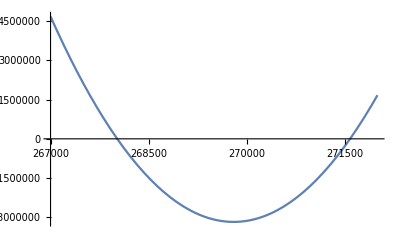

The bracket is:{268020.,268020.}

The number of iterations is: 394894

11524849/43

The bracket is:{271581.,271581.}

The number of iterations is: 1625378

7061113/26

```mathematica
F[λ_]:=λ^2-(621080767/1151)λ+(36904095215662/507);
RootFinder[F_,x0_,S_]:=Module[{xl,L,xr,R,N,avg},
xl =x0-S;
xr=x0+S;
L =F[xl];
R=F[xr];
(*N is the iterator*)
For[N=1, R* L > 0, N++;xl=xl+((-1)^N)*S*N; xr=xr+((-1)^N)*S*N;
L=F[xl];
R=F[xr];
];
avg=(xl+xr)*.5;
Print["The bracket is:",{xl,xr}];
Print["The number of iterations is: ",N];
Return[avg]
]
Plot[F[λ],{λ,267000,272000}]
Rationalize[RootFinder[F,268000,.0001],.001]
Rationalize[RootFinder[F,271500,.0001],.001]
```

```mathematica
EE1=MatrixForm[({{267362.47909-λ1, 0, 0}, {0, 271545.1749-λ1, 356.717}, {0, 356.717, 268055.839-λ1}})]
EE2=MatrixForm[({{267362.47909-λ2, 0, 0}, {0, 271545.1749-λ2, 356.717}, {0, 356.717, 268055.839-λ2}})]
EE3=MatrixForm[({{267362.47909-λ3, 0, 0}, {0, 271545.1749-λ3, 356.717}, {0, 356.717, 268055.839-λ3}})]
λ1=271581.269;
λ2=268019.7449;
λ3=271581.269;
```

(-4218.79 | 0 | 0
0 | -36.0941 | 356.717
0 | 356.717 | -3525.43)

(-657.266 | 0 | 0
0 | 3525.43 | 356.717
0 | 356.717 | 36.0941)

(-4218.79 | 0 | 0
0 | -36.0941 | 356.717
0 | 356.717 | -3525.43)

```mathematica
W=({{wx}, {wy}, {wz}});
T=W*EE
```

{{wx (-4218.79 | 0 | 0
0 | -36.0941 | 356.717
0 | 356.717 | -3525.43)},{wy (-4218.79 | 0 | 0
0 | -36.0941 | 356.717
0 | 356.717 | -3525.43)},{wz (-4218.79 | 0 | 0
0 | -36.0941 | 356.717
0 | 356.717 | -3525.43)}}